```mathematica
2-2
```

0

# Site-specific Hexagonal Walks 2

Nicholas Wheeler
7 January 2012

### Introduction

Part 1 of this notebook was originally entitled "Generalizations of the Nest Command" (29 December 2011), since the site-specific hexagonal walk problem entails evaluation of structures of a form

f_5[f_4[f_3[f_2[f_1[x]]]]]

that lies beyond the reach of the NestList command. I soon discovered, however, that to obtain my objective I would have to proceed ab initio to the construction of a compound command that uses Apply in conjunction with certain recursively defined functions. 

By the time I had reached the end of that notebook I had treated a long list of preparatory issues, but the notebook had reached such unwieldly proportions, and was making such heavy demands upon computer memory, that it seemed advisable to reserve for a separate notebook—this one—my effort to integrate the lessons thus learned into (finally!) a tentative solution of the site-specific hexagonal walk problem.

One component of this effort will be to bring uniform consistency to the variety of notations employed in Part 1.

### Basic notions

We walk on this honeycomb structure

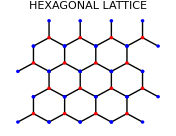

We stand alternately on red/blue nodes, and confront therefore an alternating trio of next-step options:

```mathematica
R1=N[{Cos[π/2],Sin[π/2]}];
R2=N[{Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]}];
R3=N[{Cos[π/2-8(2π)/12],Sin[π/2-8(2π)/12]}];
B1=-R1;
B2=-R2;
B3=-R3;
```

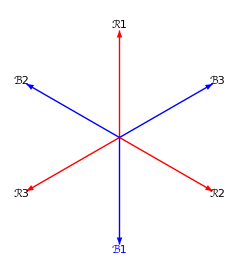

```mathematica
Graphics[{
{Thick,Red,Arrow[{{0,0},R1}]},
Text[ℛ1,1.05R1],
{Thick,Blue,Arrow[{{0,0},B3}]},
Text[ℬ3,1.05B3],
{Thick,Red,Arrow[{{0,0},R2}]},
Text[ℛ2,1.05R2],
{Thick,Blue,Arrow[{{0,0},B1}],
Text[ℬ1,1.05B1]},
{Thick,Red,Arrow[{{0,0},R3}]},
Text[ℛ3,1.05R3],
{Thick,Blue,Arrow[{{0,0},B2}]},
Text[ℬ2,1.05B2]}]
```

Next-step probabilities will be determined by the directional derivatives of a scalar field, which—with linear  corrugation in mind—we will take initially to be given by the y-invariant function

```mathematica
ψ[x_,y_]:=Sin[2π x/10]
```

of which, by

```mathematica
{D[ψ[x,y], x],D[ψ[x,y], y]}
```

{1/5 π Cos[(π x)/5],0}

the gradient is

```mathematica
gradψ[x_,y_]:={1/5 π Cos[(π x)/5],0}
```

```mathematica
DR1[x_,y_]:=Which[R1.gradψ[x,y]<0,0,R1.gradψ[x,y]⩾0,0.001+R1.gradψ[x,y]]

DR2[x_,y_]:=Which[R2.gradψ[x,y]<0,0,R2.gradψ[x,y]⩾0,0.001+R2.gradψ[x,y]]

DR3[x_,y_]:=Which[R3.gradψ[x,y]<0,0,R3.gradψ[x,y]⩾0,0.001+R3.gradψ[x,y]]

DB1[x_,y_]:=Which[B1.gradψ[x,y]<0,0,B1.gradψ[x,y]⩾0,0.001+B1.gradψ[x,y]]

DB2[x_,y_]:=Which[B2.gradψ[x,y]<0,0,B2.gradψ[x,y]⩾0,0.001+B2.gradψ[x,y]]

DB3[x_,y_]:=Which[B3.gradψ[x,y]<0,0,B3.gradψ[x,y]⩾0,0.001+B3.gradψ[x,y]]
```

```mathematica
Plot3D[DR1[x,y],{x,-20,20},{y,-20,20}]
Plot3D[DR2[x,y],{x,-20,20},{y,-20,20}]
Plot3D[DR3[x,y],{x,-20,20},{y,-20,20},PlotPoints->50]
Plot3D[DB1[x,y],{x,-20,20},{y,-20,20}]
Plot3D[DB2[x,y],{x,-20,20},{y,-20,20},PlotPoints->50]
Plot3D[DB3[x,y],{x,-20,20},{y,-20,20}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

REMARK: R1 and B1 run parallel to the y-axis, and ψ is y-invariant, which accounts for the everywhere-zero flatness of the 1st and 3rd of those figures.

### Walk-generation scheme